```mathematica
(* read in the reactions*)
d=With[
{file=FileNameJoin[{NotebookDirectory[],"data","Selected_Data.json"}]},
Import[file,"RawJSON"]];

(* select only reactions containing precursors which appear 5 or more times, and group by targets *)

allPrecursors = Counts@Flatten@Lookup["Precursors"]@d;
allowedPrecursors = KeySort@Select[GreaterEqualThan[5]]@allPrecursors;
allowedReactions=Query[Select[ContainsOnly[ #Precursors,Keys[allowedPrecursors]]&]]@d;
(* use KeyMap to extract a single target from the list, JSON only allows for strings as dictionary keys*)
allowedTargets=KeyMap[First]@Query[GroupBy["Target"],All,"Precursors"]@allowedReactions;
```

```mathematica
RandomSample[#,5]&@allowedTargets
```

<|Mn0.85Mg0.15W1O4→{{WO3,MnO,MgO}},Sm0.2Ce0.8O1.9→{{CeO2,Sm2O3},{CeO2,Sm2O3},{CeO2,Sm2O3}},Ba1Ti0.95Hf0.05O3→{{TiO2,BaCO3,HfO2}},Ru0.774Pb0.226Sr2Gd1.4Ce0.6Cu2O10→{{SrCO3,CeO2,Gd2O3,CuO,PbO,RuO2,O2},{SrCO3,CeO2,Gd2O3,CuO,PbO,RuO2,O2}},La0.4Ni0.2Co3.8Sb12→{{La,Co,Sb,Ni}}|>

```mathematica
(* export target and precursor dictionaries *)
With[
{file=FileNameJoin[{NotebookDirectory[],"data","targets.json"}]},
Export[file,#,"RawJSON","Compact"->1]&@allowedTargets];

With[
{file=FileNameJoin[{NotebookDirectory[],"data","precursors.json"}]},
Export[file,allowedPrecursors]];
```

```mathematica
(* generate 5-fold CV splits *)
SeedRandom[2024];
shuffledTargets =RandomSample@Normal@allowedTargets;

generateCVSplits[data_,iteration_Integer,folds_:5]:=With[
{splits=Partition[data,UpTo[Ceiling[Length[data]/folds]]],
file=FileNameJoin[
{NotebookDirectory[],"data","cv"<>ToString[iteration]<>".json"}]},
Export[file,#,"RawJSON","Compact"->True]&@
AssociationThread[{"train","test"}->TakeDrop[splits,{iteration}]]]

generateCVSplits[shuffledTargets,#]&/@Range[5];
```

## Visualization

```mathematica
$PlotTheme="Scientific";
singleColumn = 1.38*3.35*72;
```

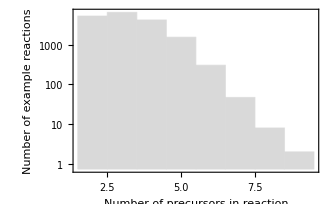

```mathematica
Histogram[ 
Query[All,Length[#Precursors]&]@allowedReactions,
{1},{"Log","Count"},
FrameLabel->{"Number of precursors in reaction","Number of example reactions"},
LabelStyle->{12,Black},PlotRange->All,
ChartStyle->LightGray,ImageSize->singleColumn]
```

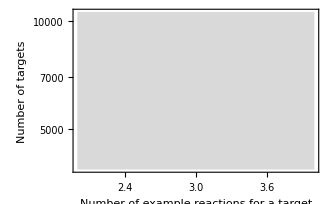

```mathematica
Histogram[ 
Map[Length]@allowedTargets,
Automatic,{"Log","Count"},
FrameLabel->{"Number of example reactions for a target","Number of targets"},
LabelStyle->{12,Black},PlotRange->All,
ChartStyle->LightGray,ImageSize->singleColumn]
```